Project root: /Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits

Tables path:  /Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables

Figures path: /Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs

Logs path:    /Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/logs

N | gauge_covariance_error | unitarity_error | min_singular_value | eigenphases | wilson_traces_r1_r2_r3
20 | 1.8048×10^-15 | 1.89877×10^-15 | 0.948464 | {0,0} | {2.,2.,2.}
40 | 3.56597×10^-15 | 4.45492×10^-15 | 0.985244 | {0,0} | {2.,2.,2.}
80 | 6.84714×10^-15 | 1.37166×10^-14 | 0.996227 | {0,0} | {2.,2.,2.}
160 | 9.54181×10^-15 | 1.44627×10^-14 | 0.999056 | {0,0} | {2.,2.,2.}
320 | 6.22795×10^-15 | 1.62802×10^-15 | 0.999763 | {0,0} | {2.,2.,2.}

N | gauge_covariance_error | unitarity_error | min_singular_value
20 | 1.8048×10^-15 | 1.89877×10^-15 | 0.948464
40 | 3.56597×10^-15 | 4.45492×10^-15 | 0.985244
80 | 6.84714×10^-15 | 1.37166×10^-14 | 0.996227
160 | 9.54181×10^-15 | 1.44627×10^-14 | 0.999056
320 | 6.22795×10^-15 | 1.62802×10^-15 | 0.999763

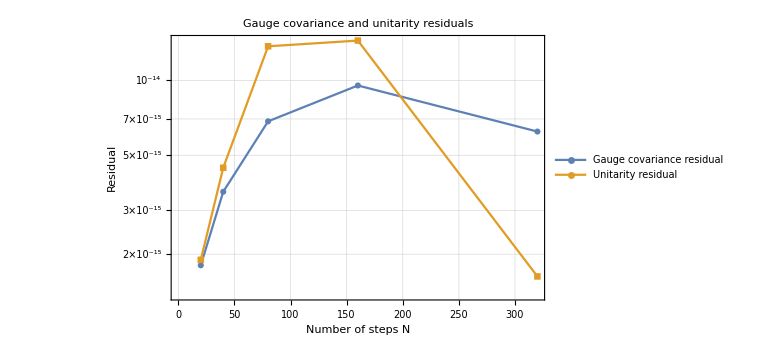

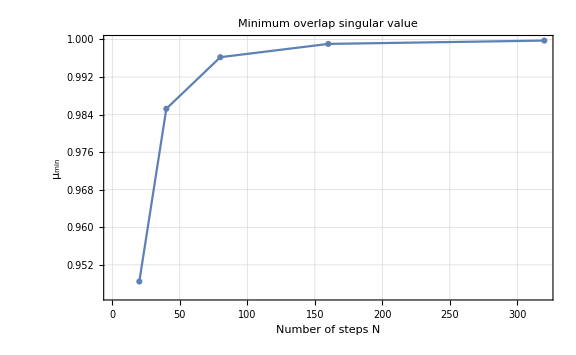

01_gauge_covariance.nb completed.

Purpose:
Validate closed-loop gauge covariance of the polar holonomy estimator.

Expected behavior:
Gauge covariance residuals should be near machine precision.
Unitarity residuals should be near machine precision.
The minimum overlap singular value should remain safely separated from zero.

Generated files:
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/01_gauge_covariance.csv
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/01_gauge_covariance_numeric.csv
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/01_gauge_covariance_residuals.pdf
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/01_gauge_covariance_residuals.png
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/01_gauge_covariance_conditioning.pdf
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/01_gauge_covariance_conditioning.png

Project root:
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits

<|max_gauge_covariance_error→9.54181×10^-15,max_unitarity_error→1.44627×10^-14,min_singular_value_over_all_runs→0.948464,full_csv→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/01_gauge_covariance.csv,numeric_csv→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/01_gauge_covariance_numeric.csv,residual_plot_pdf→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/01_gauge_covariance_residuals.pdf,conditioning_plot_pdf→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/01_gauge_covariance_conditioning.pdf,log→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/logs/01_gauge_covariance_log.txt|>

```mathematica
(*This notebook validates the closed-loop gauge covariance of the polar holonomy estimator.It generates synthetic frame data,applies random gauge transformations,checks that the reconstructed holonomy transforms by conjugation,and exports the corresponding table,figure,and log files.*)
ClearAll["Global`*"];

(*The notebook lives in notebooks/,so the project root is its parent.*)
rootPath=ParentDirectory[NotebookDirectory[]];

(*Load shared tools.Important:HolonomyTools.wl clears Global`*,so paths must be defined again after Get.*)
SetDirectory[rootPath];
Get[FileNameJoin[{rootPath,"src","HolonomyTools.wl"}]];

(*Re-define paths after loading HolonomyTools.wl.*)
rootPath=ParentDirectory[NotebookDirectory[]];
SetDirectory[rootPath];

resultsPath=FileNameJoin[{rootPath,"results"}];
tablesPath=FileNameJoin[{rootPath,"results","tables"}];
figsPath=FileNameJoin[{rootPath,"results","figs"}];
logsPath=FileNameJoin[{rootPath,"results","logs"}];

Do[If[!DirectoryQ[dir],CreateDirectory[dir,CreateIntermediateDirectories->True]],{dir,{resultsPath,tablesPath,figsPath,logsPath}}];

ClearAll[localExportCSV,localExportTXT,localExportFIG];

localExportCSV[name_String,data_]:=Module[{path},path=FileNameJoin[{tablesPath,name}];
Export[path,data,"CSV"];
path];

localExportTXT[name_String,text_String]:=Module[{path},path=FileNameJoin[{logsPath,name}];
Export[path,text,"Text"];
path];

localExportFIG[name_String,fig_]:=Module[{path},path=FileNameJoin[{figsPath,name}];
Export[path,fig];
path];

SeedRandom[12345];

Print["Project root: ",rootPath];
Print["Tables path:  ",tablesPath];
Print["Figures path: ",figsPath];
Print["Logs path:    ",logsPath];

(*Gauge covariance validation data*)

nList={20,40,80,160,320};

gaugeRows=Table[Module[{frames,overlaps,H,gaugeErr,unitErr,muMin,phases,traces},frames=sampledFrames[nSteps];
overlaps=overlapMatrices[frames];
H=discreteHolonomyFromFrames[frames];
gaugeErr=gaugeCovarianceError[frames];
unitErr=unitaryError[H];
muMin=minOverlapSingularValue[overlaps];
phases=eigenphases[H];
traces=wilsonTraces[H,3];
{nSteps,gaugeErr,unitErr,muMin,phases,traces}],{nSteps,nList}];

gaugeTable=Prepend[gaugeRows,{"N","gauge_covariance_error","unitarity_error","min_singular_value","eigenphases","wilson_traces_r1_r2_r3"}];

Grid[gaugeTable,Frame->All,Alignment->Left,ItemSize->All]

(*Compact numeric table for plotting*)

gaugeNumericRows=gaugeRows[[All,{1,2,3,4}]];

gaugeNumericTable=Prepend[gaugeNumericRows,{"N","gauge_covariance_error","unitarity_error","min_singular_value"}];

Grid[gaugeNumericTable,Frame->All,Alignment->Left,ItemSize->All]

(*Plot:gauge covariance and unitarity residuals*)

residualPlotData={gaugeRows[[All,{1,2}]],gaugeRows[[All,{1,3}]]};

residualPlot=ListLogPlot[residualPlotData,Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Number of steps N","Residual"},PlotLegends->{"Gauge covariance residual","Unitarity residual"},GridLines->Automatic,ImageSize->Large,PlotLabel->"Gauge covariance and unitarity residuals"];

residualPlot

(*Plot:conditioning diagnostic*)

conditioningPlot=ListLinePlot[gaugeRows[[All,{1,4}]],PlotMarkers->Automatic,Frame->True,FrameLabel->{"Number of steps N","\!\(\*SubscriptBox[\(μ\), \(min\)]\)"},GridLines->Automatic,ImageSize->Large,PlotLabel->"Minimum overlap singular value"];

conditioningPlot

(*Export results*)

csvPathFull=localExportCSV["01_gauge_covariance.csv",gaugeTable];

csvPathNumeric=localExportCSV["01_gauge_covariance_numeric.csv",gaugeNumericTable];

figPathResidualPDF=localExportFIG["01_gauge_covariance_residuals.pdf",residualPlot];

figPathResidualPNG=localExportFIG["01_gauge_covariance_residuals.png",residualPlot];

figPathConditioningPDF=localExportFIG["01_gauge_covariance_conditioning.pdf",conditioningPlot];

figPathConditioningPNG=localExportFIG["01_gauge_covariance_conditioning.png",conditioningPlot];

logText=StringRiffle[{"01_gauge_covariance.nb completed.","","Purpose:","Validate closed-loop gauge covariance of the polar holonomy estimator.","","Expected behavior:","Gauge covariance residuals should be near machine precision.","Unitarity residuals should be near machine precision.","The minimum overlap singular value should remain safely separated from zero.","","Generated files:",csvPathFull,csvPathNumeric,figPathResidualPDF,figPathResidualPNG,figPathConditioningPDF,figPathConditioningPNG,"","Project root:",rootPath},"\n"];

logPath=localExportTXT["01_gauge_covariance_log.txt",logText];

Print[logText];

(*Final validation summary*)

summary=<|"max_gauge_covariance_error"->Max[gaugeRows[[All,2]]],"max_unitarity_error"->Max[gaugeRows[[All,3]]],"min_singular_value_over_all_runs"->Min[gaugeRows[[All,4]]],"full_csv"->csvPathFull,"numeric_csv"->csvPathNumeric,"residual_plot_pdf"->figPathResidualPDF,"conditioning_plot_pdf"->figPathConditioningPDF,"log"->logPath|>;

summary
```